```mathematica
RootPath=NotebookDirectory[];
(*RootPath="~/Desktop/Paper With Tom/Mathematica"*)
FileNameJoin[{RootPath,"SciDraw-0.0.7","packages"}];
AppendTo[$Path,%];
Get["SciDraw`"]
```

~/Desktop/Paper With Tom/Mathematica

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.5 (October 11, 2014)
View color paletteVisit home page  -Graphics-

```mathematica
(* Options for all plots *)
TexWidthPoints=468;
LeftMarginSizeInches=0.5;
RightMarginSizeInches=0.5;
BottomMarginSizeInches=.45;
TopMarginSizeInches=.1;
MarginSizeInches={{LeftMarginSizeInches,RightMarginSizeInches},{BottomMarginSizeInches,TopMarginSizeInches}};
(*CanvasWidth=TexWidthPoints/72.0-2*MarginSizeInches;*)
CanvasWidth=TexWidthPoints/72.0-2*0.5;
CanvasHeight=CanvasWidth/GoldenRatio;
TextPoint=10;
GridLineColor=LightGray;
ColorPalette={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
SinglePlotCanvasWidth=1/2 CanvasWidth;
SinglePlotCanvasHeight=CanvasHeight/2;
(*2/2.1(*xpanelgap*)(CanvasHeight-BottomMarginSizeInches-TopMarginSizeInches)/2+BottomMarginSizeInches+TopMarginSizeInches;*)
```

```mathematica
(* Some plot styles *)
DefineStyle["FirebrickLine",{DataLine->{LineDashing->None,Color->Firebrick,LineThickness->1},DataSymbol->{Show->False}}];
DefineStyle["BlackLine",{DataLine->{LineDashing->None,Color->Black,LineThickness->1},DataSymbol->{Show->False}}];
```

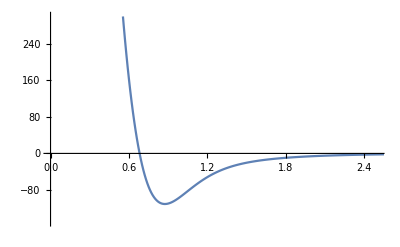

```mathematica
OneSZero=Import["~/Documents/School/Thesis/Introduction/Figures/av18/1S0.out"];
ListPlot[OneSZero,PlotRange->{{0,2.5},{-150,300}},Joined->True]
```

```mathematica
(* 1 GeV^-1 = .197 Fermi *)
mπ=.197/(139.57/1000)
protonRadius = .8768
```

1.41148

0.8768

```mathematica
OneSZeroFig=Figure[
FigurePanel[{(* Plots *)
FigRule[Horizontal,0,All,LineColor->Black];
FigRule[Vertical,mπ,All,LineColor->Black,LineDashing->Dashed,RightLabel->"λ_π",RightFontSize->10,RightTextNudge->{10,20},RightTextOrientation->Horizontal];
FigRule[Vertical,protonRadius,All,LineColor->Black,LineDashing->Dashed,RightLabel->"R_E",RightFontSize->10,RightTextNudge->{10,20},RightTextOrientation->Horizontal];
DataPlot[OneSZero,Style->"FirebrickLine"];
},

(* axes *)
XPlotRange->{0,2.5},
XFrameLabel->"r (fm)",

YPlotRange->{-150,300},
YFrameLabel->"V(r) (MeV)",

FontSize->TextPoint
],
CanvasSize->{SinglePlotCanvasWidth,SinglePlotCanvasHeight},CanvasMargin->MarginSizeInches]
Export [FileNameJoin[{RootPath,"../","OneSZero.eps"}],OneSZeroFig];
```

-Graphics-

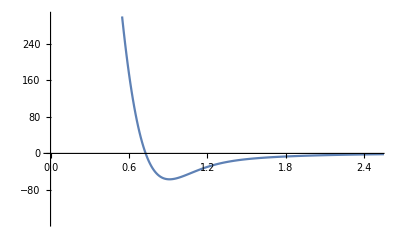

```mathematica
ThreeSOne=Import["~/Documents/School/Thesis/Introduction/Figures/av18/3S1.out"];ListPlot[ThreeSOne,PlotRange->{{0,2.5},{-150,300}},Joined->True]
```

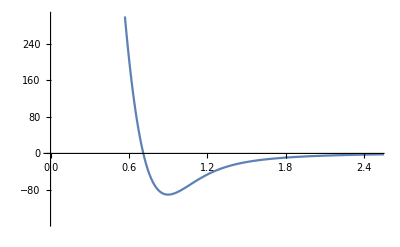

```mathematica
OnePOne=Import["~/Documents/School/Thesis/Introduction/Figures/av18/1P1.out"];ListPlot[OnePOne,PlotRange->{{0,2.5},{-150,300}},Joined->True]
```